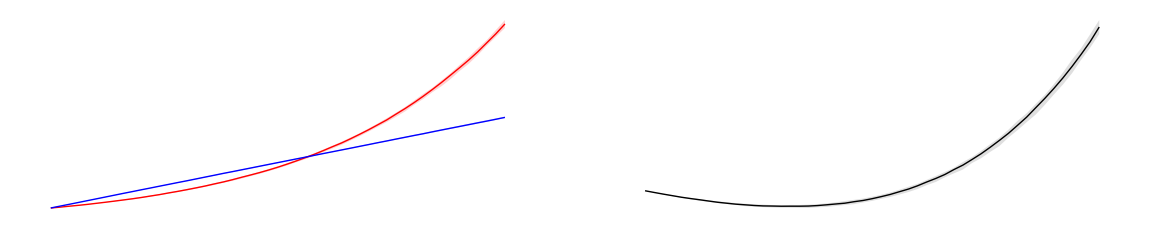

PNG saved to: /Volumes/External/Ruliology/complexity_gap_two_panel.png

PDF saved to: /Volumes/External/Ruliology/complexity_gap_two_panel.pdf

Working directory: /Volumes/External/Ruliology/

```mathematica
ClearAll["Global`*"]

(* =========================1. Parameters=========================*)
tMax=50;
σRatio=0.015;
nRuns=50;
tVals=Range[0,tMax];

(* =========================2. Simulate in log space=========================*)
bioLogPop=Table[FoldList[#1+(0.08+RandomReal[{-1,1}*σRatio])*Exp[#2*0.05]&,0,Range[tMax]],{nRuns}];

aiLogPop=Table[FoldList[#1+(0.18+RandomReal[{-1,1}*σRatio])&,0,Range[tMax]],{nRuns}];

(* =========================3. Summary statistics=========================*)
bioMedian=Median/@Transpose[bioLogPop];
bioQ10=Quantile[#,0.10]&/@Transpose[bioLogPop];
bioQ90=Quantile[#,0.90]&/@Transpose[bioLogPop];

aiMedian=Median/@Transpose[aiLogPop];
aiQ10=Quantile[#,0.10]&/@Transpose[aiLogPop];
aiQ90=Quantile[#,0.90]&/@Transpose[aiLogPop];

gapLogPop=bioLogPop-aiLogPop;
gapMedian=Median/@Transpose[gapLogPop];
gapQ10=Quantile[#,0.10]&/@Transpose[gapLogPop];
gapQ90=Quantile[#,0.90]&/@Transpose[gapLogPop];

(* =========================4. Helper for shaded bands=========================*)
band[lo_,hi_,x_]:=Polygon@Join[Transpose[{x,lo}],Reverse[Transpose[{x,hi}]]];

commonStyle=Sequence[Background->White,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.002]],LabelStyle->Directive[Black,14],TicksStyle->Directive[Black,12],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],ImagePadding->{{70,20},{55,45}},PlotRangePadding->Scaled[0.03]];

(* =========================5. Panel A=========================*)
panelA=Show[Graphics[{{Red,Opacity[0.18],band[bioQ10,bioQ90,tVals]},{Blue,Opacity[0.18],band[aiQ10,aiQ90,tVals]}}],ListLinePlot[{Transpose[{tVals,bioMedian}],Transpose[{tVals,aiMedian}]},Joined->True,PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},FrameLabel->{Style["Evolutionary Step (t)",Black,14],Style["Log System Complexity",Black,14]},PlotLabel->Style["A. Biological vs. Artificial Scaling",Black,16,Bold],Epilog->{Black,Thick,Arrow[{{35,aiMedian[[36]]},{35,bioMedian[[36]]}}],Inset[Style["Complexity Gap",Black,12,Bold,Background->White],{39,(bioMedian[[36]]+aiMedian[[36]])/2}]},Evaluate@commonStyle,PlotRange->All,ImageSize->520]];

(* =========================6. Panel B=========================*)
panelB=Show[Graphics[{{Gray,Opacity[0.25],band[gapQ10,gapQ90,tVals]}}],ListLinePlot[{Transpose[{tVals,gapMedian}]},Joined->True,PlotStyle->{Directive[Black,Thick]},FrameLabel->{Style["Evolutionary Step (t)",Black,14],Style["Log(Biological / Artificial Complexity)",Black,14]},PlotLabel->Style["B. Growth of the Complexity Gap",Black,16,Bold],Evaluate@commonStyle,PlotRange->All,ImageSize->520]];

(* =========================7. Final figure=========================*)
finalFigure=GraphicsRow[{panelA,panelB},Spacings->25,Background->White,ImageSize->1150];

finalFigure

(* =========================8. Export with explicit paths=========================*)
exportDir=If[Head[NotebookDirectory[]]===String,NotebookDirectory[],Directory[]];

pngPath=FileNameJoin[{exportDir,"complexity_gap_two_panel.png"}];
pdfPath=FileNameJoin[{exportDir,"complexity_gap_two_panel.pdf"}];

pngResult=Export[pngPath,finalFigure,ImageResolution->300];
pdfResult=Export[pdfPath,finalFigure];

Print["PNG saved to: ",pngResult];
Print["PDF saved to: ",pdfResult];
Print["Working directory: ",exportDir];
```

```mathematica
(* =========================5. Panel A=========================*)panelA=Show[ListLinePlot[{Transpose[{tVals,bioMedian}],Transpose[{tVals,aiMedian}]},Joined->True,PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},PlotRange->All,ImageSize->520],Graphics[{{Red,Opacity[0.18],band[bioQ10,bioQ90,tVals]},{Blue,Opacity[0.18],band[aiQ10,aiQ90,tVals]},{Black,Thick,Arrow[{{35,aiMedian[[36]]},{35,bioMedian[[36]]}}]},Inset[Style["Complexity Gap",Black,12,Bold,Background->White],{39,(bioMedian[[36]]+aiMedian[[36]])/2}]}],Background->White,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->All,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],GridLines->{Range[0,50,10],Automatic},GridLinesStyle->Directive[GrayLevel[0.8],Thin],FrameLabel->{Style["Evolutionary Step (t)",Black,14],Style["Log System Complexity",Black,14]},PlotLabel->Style["A. Biological vs. Artificial Scaling",Black,16,Bold],ImagePadding->{{70,20},{55,45}},PlotRangePadding->Scaled[0.03]];

(* =========================6. Panel B=========================*)
panelB=Show[ListLinePlot[{Transpose[{tVals,gapMedian}]},Joined->True,PlotStyle->{Directive[Black,Thick]},PlotRange->All,ImageSize->520],Graphics[{{Gray,Opacity[0.25],band[gapQ10,gapQ90,tVals]}}],Background->White,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->All,TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],GridLines->{Range[0,50,10],Automatic},GridLinesStyle->Directive[GrayLevel[0.7],AbsoluteThickness[1]]
FrameLabel->{Style["Evolutionary Step (t)",Black,14],Style["Log(Biological / Artificial Complexity)",Black,14]},PlotLabel->Style["B. Growth of the Complexity Gap",Black,16,Bold],ImagePadding->{{70,20},{55,45}},PlotRangePadding->Scaled[0.03]];
```

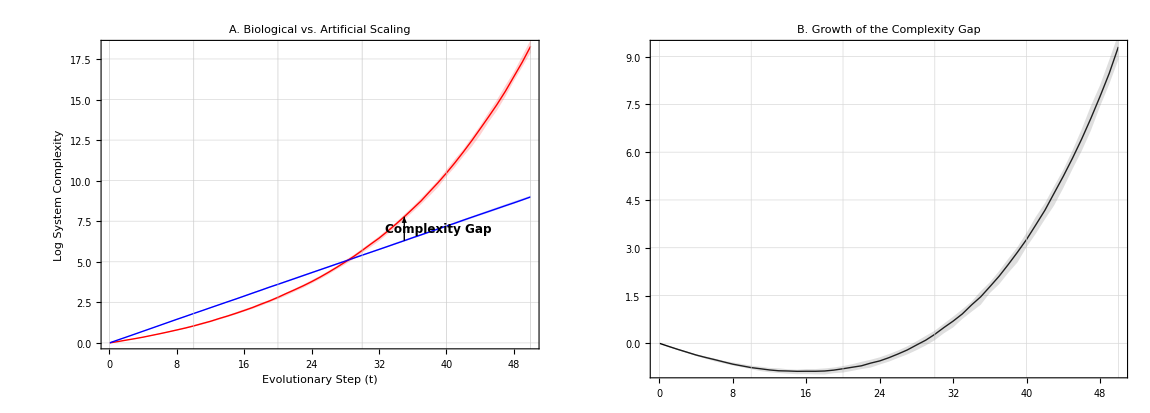

PNG saved to: /Volumes/External/Ruliology/complexity_gap_two_panel.png

PDF saved to: /Volumes/External/Ruliology/complexity_gap_two_panel.pdf

Working directory: /Volumes/External/Ruliology/

```mathematica
finalFigure=GraphicsRow[{panelA,panelB},Spacings->25,Background->White,ImageSize->1150];

finalFigure

exportDir=If[Head[NotebookDirectory[]]===String,NotebookDirectory[],Directory[]];

pngPath=FileNameJoin[{exportDir,"complexity_gap_two_panel.png"}];
pdfPath=FileNameJoin[{exportDir,"complexity_gap_two_panel.pdf"}];

pngResult=Export[pngPath,finalFigure,ImageResolution->300];
pdfResult=Export[pdfPath,finalFigure];

Print["PNG saved to: ",pngResult];
Print["PDF saved to: ",pdfResult];
Print["Working directory: ",exportDir];
```